# Analyze Simulation Data

## Set ℓs

```mathematica
rnd=Function[N[10^-6 IntegerPart[Round[10^6 #1,10^6#2]]]];   (* corrects for machine precision error in function indexing *)

"lmin ="<>ToString[lmin=1]
"lmax ="<>ToString[lmax=10]
"lspc ="<>ToString[lspc=(*{1,2,3,4,7,13,14,15,16,17}*)Range[10]]
(*"lmin ="SetterBar[Dynamic[lmin],Range[10]]
"lmax ="SetterBar[Dynamic[lmax],Range[10]]
"lspc =" TogglerBar[Dynamic[lspc],Range[10]]
"lspc ="Dynamic[lspc=Sort[lspc]]*)
```

lmin =1

lmax =10

lspc ={1, 2, 3, 4, 5, 6, 7, 8, 9, 10}

## Import Radial Solutions

## Set Directory

```mathematica
(*SetDirectory["C:\\Users\\joebr\\Documents\\QPO Research\\Mathematica Code\\Hyalite\\FullSimulationc3"];*)
(*SetDirectory["C:\\Users\\joebr\\Documents\\QPO Research\\Mathematica Code\\Hyalite\\c10\\ic0p5sr1o8rp1p1"];*)
(*SetDirectory["C:\\Users\\joebr\\Documents\\QPO Research\\Mathematica Code\\Hyalite\\Contour\\Simulation\\Out"];*)
(*SetDirectory["C:\\Users\\joebr\\Documents\\QPO Research\\Mathematica Code\\Hyalite\\Contour\\c10\\1900Fit"];*)
SetDirectory["C:\\Users\\joebr\\Documents\\QPO Research\\Mathematica Code\\Hyalite\\Contour\\c370\\t100"];FileNames[]
```

{F2cC370ic0p7sr1o12rp1time100s0p01l10.Mx,F2cC370ic0p7sr1o12rp1time100s0p01l1.Mx,F2cC370ic0p7sr1o12rp1time100s0p01l2.Mx,F2cC370ic0p7sr1o12rp1time100s0p01l3.Mx,F2cC370ic0p7sr1o12rp1time100s0p01l4.Mx,F2cC370ic0p7sr1o12rp1time100s0p01l5.Mx,F2cC370ic0p7sr1o12rp1time100s0p01l6.Mx,F2cC370ic0p7sr1o12rp1time100s0p01l7.Mx,F2cC370ic0p7sr1o12rp1time100s0p01l8.Mx,F2cC370ic0p7sr1o12rp1time100s0p01l9.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l10.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l1.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l2.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l3.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l4.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l5.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l6.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l7.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l8.Mx,F2cC370ic1p0sr1o12rp1time100s0p01l9.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l10.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l1.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l2.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l3.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l4.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l5.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l6.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l7.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l8.Mx,F2cC370ic1p3sr1o12rp1time100s0p005l9.Mx}

## Import and Set F1,F2

### Radial and Temporal Discretization

```mathematica
Δr=.025`64;              (* radial spacing *)
Ri=Δr/4;             (* inner radial bound *)
Rb=3.`64;             (* outer radial bound *)
Rp=1.`64;           (* radial probe point *)
ti=8132.`64(*10000.`64*);      (* inital time *)
tf=8945.`64(*11000.`64*);    (* final time *)
Δt=.01`64;   (* temporal spacing *)
```

### Import and Set across ℓs

```mathematica
Do[
importdata2[li]=Import[
"F2cC370ic0p7sr1o12rp1time100s0p01l"
(*"F2cC10ic0p9sr1o20rp1p1001time100s0p01l"*)
(*"F2cC10ic25916Yrp1p1001time100s0p01l"*)
(*"FcC2ic0p5sr1o8rb3r0p05time10s0p05l"*)
(*"FcC2ic1p5sr1o8rb3r0p025time15s0p025l"*)
(*"F2c100ic1p0sr1o8rp1p10001time20s0p0005l"*)<>ToString[li]<>".Mx"];
Do[F2[l,Rp(*rnd[r,Δr/4]*),rnd[t,Δt]]=importdata2[l][[1,1(*(r-Ri)/Δr+1//Round*),(t-ti)/Δt+1//Round,2]]
(*Print[{l,r,t}]*),{l,li,li},{r,Rp,Rp}(*{r,Ri,Rb,Δr}*),{t,ti,tf,Δt}],
{li,lspc}]
```

```mathematica
Dimensions[importdata2[4]]
```

{1,1,81301,2}

```mathematica
imdt=Table[{Δt(t-1),Re[importdata2[l][[1,1,t,2]]]},{l,lspc},{t,1001}];
```

```mathematica
Dimensions[imdt]
```

{15,1001,2}

```mathematica
Manipulate[ListLinePlot[imdt[[Position[lspc,l][[1,1]],;;,;;]],PlotRange->All(*{-.04,.05}*),PlotStyle->{Directive[Black,Thick]},Frame->True(*,PlotMarkers->{"◆", 8}*),AspectRatio->1/8,ImageSize->Full],{l,lspc,SetterBar}(*,{t,1,60,1}*)]
```

#### Scale: Time Series Plots

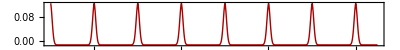

```mathematica
c1001=ListLinePlot[{Re[imdt[[(*l*)1,1001;;2501]]](*Re[importdata2[l][[1,1,1;;4000]]]*)(*,importdata10o[l][[1,1,3500;;4000]]*)},PlotRange->All(*{-.04,.05}*),PlotStyle->{Directive[(*Black*)Darker[Red],Thick],Directive[Blue,Thin]},Frame->True(*,PlotMarkers->{"◆", 8}*),AspectRatio->1/8,ImageSize->Full]
```

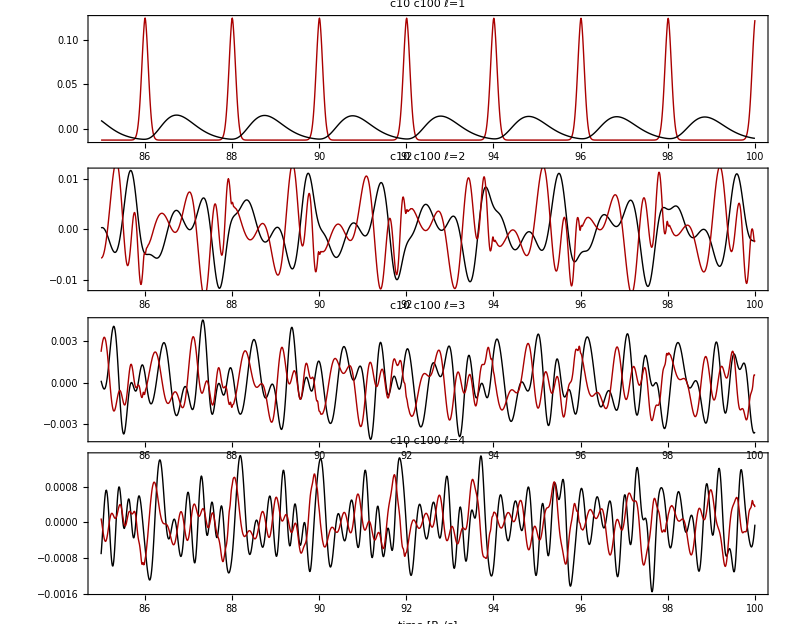

```mathematica
GraphicsColumn[{Show[c1001l,c101l,PlotLabel-> "ℓ=1"Style["c10   ",Black,Bold]Style["c100   ",Darker[Red],Bold]],
Show[c102l,c1002l,PlotLabel-> "ℓ=2"Style["c10   ",Black,Bold]Style["c100   ",Darker[Red],Bold]],
Show[c103l,c1003l,PlotLabel-> "ℓ=3"Style["c10   ",Black,Bold]Style["c100   ",Darker[Red],Bold]],
Show[c104l,c1004l,PlotLabel-> "ℓ=4"Style["c10   ",Black,Bold]Style["c100   ",Darker[Red],Bold],FrameLabel->"time [R_s/c]"]},Automatic,-22,ImageSize->800]
```

```mathematica
imds=Table[{imdt[[1,t,1]],Sum[imdt[[l,t,2]],{l,1,15}]},{t,10001}];
```

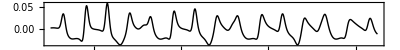

```mathematica
c10tot=ListLinePlot[{Re[imds[[1001;;2501]]]},PlotRange->All(*{-.04,.05}*),PlotStyle->{Directive[Black(*Darker[Green]*),Thick],Directive[Blue,Thin]},Frame->True(*,PlotMarkers->{"◆", 8}*),AspectRatio->1/8,ImageSize->Full]
```

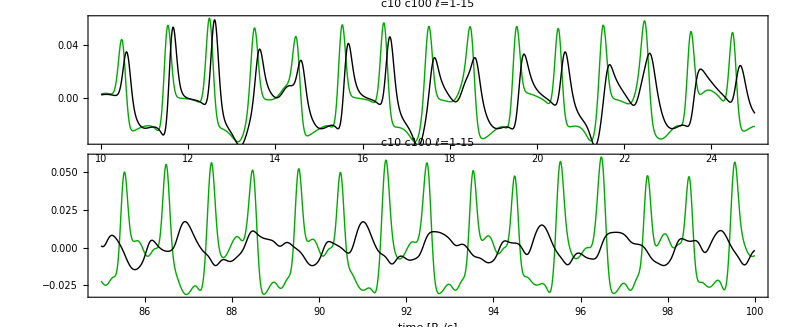

```mathematica
GraphicsColumn[{Show[c100tot,c10tot,PlotLabel-> "ℓ=1-15"Style["c10   ",Black,Bold]Style["c100   ",Darker[Green],Bold]],
Show[c100totl,c10totl,PlotLabel-> "ℓ=1-15"Style["c10   ",Black,Bold]Style["c100   ",Darker[Green],Bold],FrameLabel->"time [R_s/c]"]},Automatic,-22,ImageSize->800]
```

```mathematica
SetDirectory["C:\\Users\\joebr\\OneDrive\\Documents\\QPO Research\\Mathematica Plots\\ScalePlots"]
```

C:\Users\joebr\OneDrive\Documents\QPO Research\Mathematica Plots\ScalePlots

```mathematica
Export["OnScalec10c100l1234late.jpg",%276,ImageResolution->400]
```

OnScalec10c100l1234late.jpg

### Combine Time Segments

```mathematica
importdat2=Import["F2C10ic0p5sr1o8rp1p1time100s0p01lallcomb.Mat"];
%//Dimensions
```

{10,1,10001}

```mathematica
Take[importdat2[[1,1,;;]],2]
Take[importdat2[[1,1,;;]],-2]
```

{-0.0456008,0.00887907}

{-0.00140474,-0.000762767}

```mathematica
Do[F2[l,r,rnd[t,Δt]]=importdat2[[Position[lspc,l][[1,1]],1,t/Δt+1-ti/Δt//Round]],{l,lspc}(*,{r,Rs,Rb,Δr}*),{r,Rp,Rp},(*{t,0.,20.(*-Δt*),Δt}*){t,ti,tf,Δt}]
```

```mathematica
With[{lp=3},
{F2[lp,1.1,0.],
F2[lp,1.1,40.],
F2[lp,1.1,40.01],
F2[lp,1.1,70.],
F2[lp,1.1,70.01],
F2[lp,1.1,100.],
F2[lp,1.1,100.01]}//TableForm
]
```

3.21884×10^-6
-0.013113
-0.0147614
-0.00210232
-0.00167946
0.00259973
F2[3,1.1,100.01]

#### Clear F2

```mathematica
Do[F2[l,r,rnd[t,Δt]]=.,{l,1,10},{r,Rp,Rp},{t,0,40.,Δt}]//Quiet
```

### Export Combined Data

```mathematica
(*F1table=Table[F1[l,r,rnd[t,Δt]],{l,lmin,lmax},{r,Ri,Rs,Δr},{t, ti, tf, Δt}];*)
F2table=Table[F2[l,r,rnd[t,Δt]],{l,lspc(*lmin,lmax*)}(*,{r,Rs,Rb,Δr}*),{r,Rp,Rp},{t, ti, tf, Δt}];
%//Dimensions
```

{10,1,4001}

```mathematica
(*Export["F1ic1p5r0p05time12s0p05l15in.Mat",F1table]*)
```

```mathematica
Export["F2C10ic1p5sr1o8rp1p1time40s0p01lallcomb.Mat",F2table]
```

F2C10ic1p5sr1o8rp1p1time40s0p01lallcomb.Mat

## Set Simulation Parameters

### Physical Parameters

```mathematica
Rs=1.`64;      (* stellar surface *)
c1=1;               (* internal wave speed *)
c2=370;             (* external wave speed *)
μ1=1;              (* internal shear modulus *)
μ2=1/11;              (* external shear modulus *)

α=(c2 μ1 -c1 μ2)/(c2 μ1 +c1 μ2)    (* reflection coefficient *)
```

0.9995206554536790774752106724685190334100987141731157962942397322588

### Import Eigenfrequencies

```mathematica
SetDirectory["C:\\Users\\joebr\\Documents\\QPO Research\\Mathematica Code\\Spherical Eigenvalues"];
FileNames[]
(*c3EigFreq=Import["c3mu0evsl50n50.Mat"];
Dimensions[%]
c10EigFreq=Import["c10mu0evsl50n50.Mat"];
Dimensions[%]
c100EigFreq=Import["c100mu0evsl50n50.Mat"];
Dimensions[%]*)
```

{c1000evsl30n100.mx,c1000XMl30.m,c1000XMl30sc.Mx,c100ExtraModes20.m,c100ExtraModes30.m,c100ExtraModes40.m,c100ExtraModes50.m,c100ExtraModes.m,c100ExtraModes.nb,c100mu0evsl30n150.mx,c100mu0evsl30n50.mx,c100mu0evsl50n50.Mat,c100mu0evsl50n50.mx,c100mu0evsl50n50np48.mx,c100testevsl4n47.mx,c100XMl10.Mx,c100XMl20.Mx,c100XMl30.Mx,c100XMl50.Mx,c10mu0evsl50n50.Mat,c10mu0evsl50n50.mx,c10mu0evsl50n50np48.mx,c370evsl10n50.mx,c370evsl10n51.mx,c370evsl25n101.mx,c370evsl25n105a.mx,c370evsl25n105.mx,c370XMl25.m,c370XMl25.Mx,c370XMl25o.Mx,c3mu0evsl50n50.Mat,c3mu0evsl50n50.mx,c3mu0evsl50n50np48.mx,c580evsl25n105.mx,c580XMl25.m,c580XMl25.Mx,c5evsl20n20.Mx,ComplexModes.nb,CoupledRootFinder.nb,CRFc1000l30n100.m,CRFc100l30n150.m,CRFc100l30n50.m,CRFc100l30n50nb.nb,CRFc100l30n50p.m,CRFc100l50n50.m,CRFc10l50n50.m,CRFc370l25n100aided.m,CRFc370l25n100a.m,CRFc370l25n100a.nb,CRFc370l25n100.m,CRFc3l50n50.m,CRFc580l25n100.m,EFJob.sh,evaluesc10,evaluesc100,evaluesc1000,evaluesc100l20n50,evaluesc2,evaluesc370,evaluesc370l10,evaluesc5,evaluesc580,RootFinder.nb,SphericalEigenvalues.nb,VariableMu}

```mathematica
<<evaluesc10
```

```mathematica
<<evaluesc100
```

```mathematica
<<evaluesc1000
```

```mathematica
<<evaluesc580
```

```mathematica
<<evaluesc370
```

#### Plot Eigenfrequencies

```mathematica
levs=Table[ReIm[ww[If[OddQ[l],n-1,n],l]],{l,30},{n,1,If[OddQ[l],151,150]}];
```

```mathematica
ListPlot[levs,PlotRange->All,PlotMarkers->{"●",7},Frame->True,ImageSize->Large]
ListLogPlot[levs,PlotRange->All,PlotMarkers->{"●",5},Frame->True,ImageSize->Large]
ListLogPlot[levs,PlotRange->{1*^-10,1*^-1},PlotMarkers->{"●",5},Frame->True,ImageSize->Large]
```

## Calculate Angular Solutions

### θ - Orthogonality Integrals

```mathematica
Do[
TH1[l,0]=NIntegrate[√((2l+1)/(4π))D[(fθ[θ]), θ]((l+1)LegendreP[l+1,0,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,0,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2[l,0]=NIntegrate[√((2l+1)/(4π))fθ[θ]/Sin[θ] LegendreP[l,0,Cos[θ]],{θ,0,π},AccuracyGoal->Automatic];

Do[
TH1[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))D[(fθ[θ]), θ]((l+1-m)LegendreP[l+1,m,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,m,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))fθ[θ]/Sin[θ] LegendreP[l,m,Cos[θ]],{θ,0,π},AccuracyGoal->Automatic];
TH1[l,-m]=(-1)^m TH1[l,m];
TH2[l,-m]=(-1)^m TH2[l,m];
,{m,1,l}]
,{l,lspc}]//Timing
```

{4.70313,Null}

### ϕ - Orthogonality Integrals

```mathematica
PH1[0]=NIntegrate[fϕ[ϕ],{ϕ,0,2π}];
PH2[0]=0;
Do[
PH1[m]=NIntegrate[fϕ[ϕ] Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];
PH2[m]=NIntegrate[-ⅈ m D[(fϕ[ϕ]), ϕ]Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];

PH1[-m]=Conjugate[PH1[m]];
PH2[-m]=Conjugate[PH2[m]];
,{m,1,Max[lspc]}];//Timing
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {2.88379}. NIntegrate obtained -2.91434×10^-16 and 3.3226×10^-16 for the integral and error estimates.

{0.3125,Null}

### Sum Angular Solutions G

```mathematica
Do[
G[l][θ_,ϕ_]=Sum[(TH1[l,m]PH1[m]+TH2[l,m]PH2[m])√((2l+1)/(4π))√(((l-m)!)/((l+m)!))Exp[I m ϕ]/Sin[θ]((l+1-m)LegendreP[l+1,m,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,m,Cos[θ]]),{m,-l,l}];
,{l,lspc}];
(*ListPlot[Table[G[l][θm,π],{l,lspc}],Joined->True,PlotMarkers->{"□",8},PlotRange->All]*)
```

#### Amplitude distribution vs ℓ

```mathematica
thph=Table[Abs[G[l][4.1,π+.1]],{l,lspc}]//Chop
```

{0,0.0860531,0.019143,3.70796,17.3947,38.6063,50.406,39.3718,14.1367,5.16096}

```mathematica
θm=4.1;
```

```mathematica
GraphicsRow[{ListPlot[Table[G[l][θm,π+.1],{l,lspc}],Joined->True,PlotMarkers->{"□",8},PlotRange->All,Frame->True,FrameLabel->{"ℓ","amplitude"},GridLines->{{},{0}},PlotLabel->"Angular",ImageSize->350],
ListPlot[Table[Mean[Table[Abs[F2[l,Rp,rnd[t,Δt]]],{t,ti+1,ti+3,Δt}]],{l,lspc}],Joined->True,PlotMarkers->{"□",8},PlotRange->All,Frame->True,FrameLabel->{"ℓ","amplitude"},GridLines->{{},{0}},PlotLabel->"Radial"],
ListPlot[Table[G[l][θm,π+.1]Mean[Table[Abs[F2[l,Rp,rnd[t,Δt]]],{t,ti+1,ti+3,Δt}]],{l,lspc}],Joined->True,PlotMarkers->{"□",8},PlotRange->All,Frame->True,FrameLabel->{"ℓ","amplitude"},GridLines->{{},{0}},PlotLabel->"Combined"]},-5]
```

### Sum Angular Solutions H

```mathematica
Do[
H[l][θ_,ϕ_]=Sum[(TH1[l,m]PH1[m]+TH2[l,m]PH2[m])√((2l+1)/(4π))√(((l-m)!)/((l+m)!))(-I m)Exp[I m ϕ]/Sin[θ] LegendreP[l,m,Cos[θ]],{m,-l,l}];
,{l,lspc}];
```

## Full Solution

```mathematica
Uϕ2l[l_,r_,θ_,ϕ_,t_]=F2[l,r,t]G[l][θ,ϕ];
Uθ2l[l_,r_,θ_,ϕ_,t_]=F2[l,r,t]H[l][θ,ϕ];
```

```mathematica
τxsyml[l_,r_,θ_,t_]=F2[l,r,t]Axsym[l][θ];
```

```mathematica
τxl[l_,r_,θ_,t_]=F2[l,r,t]Ax[l][θ];
```

### Set Physical Scale of Amplitude and Energy

```mathematica
E0=Etot
```

3221.524183688151434

```mathematica
(*uamp=6.85351 10^5 (*centimeters*);
Ei=E0(uamp/10^6)^2 Quantity[1*^47,"Ergs"]*)
Ei=10^46(*ergs*);
uamp=10^6 √(Ei/E0 10^-47)
```

5571.463658462679643

### Field Fluctuations for Specified Location

```mathematica
θs=(*ArcSin[√(1/10.)]*)θm
θs/Degree
τ=.0123//N (* Physical Timescale*)
```

θm

θm/°

0.0123

```mathematica
(*Uϕ2lts=Table[{t,(1(*uamp*))/(1(*10^6*))Re[Uϕ2l[l,Rp,θs,π,rnd[t,Δt]]]},{t,ti,tf,Δt},{l,lspc}];*)
(*Uθ2lts=Table[{t,Uθ2l[l,Rp,1.33,.9π,rnd[t,Δt]]},{t,ti,tf,Δt},{l,1,10}];*)
```

```mathematica
Do[Gv[l]=G[l][π/2(*1.873*),π+σϕ],{l,lspc}];
(*Do[Gv[l]=√((G[l][θ,ϕ])^2+(H[l][θ,ϕ])^2)/.{θ->7.8/9 π/2,ϕ->4π/4},{l,lspc}]*)
Uϕ2lts=Table[{t,uamp/((*1*)10^6)Re[F2[l,Rp,rnd[t,Δt]]Gv[l]]},{t,ti,tf,Δt},{l,lspc}];
(*Uϕ2lts=Table[{t,uamp/((*1*)10^6)Re[F2aD[l][[1,1,t]]]Gv[l]},{t,20001},{l,lspc}];*)
```

```mathematica
%//Dimensions
```

{81301,10,2}

```mathematica
τs=Sum[τxlts[[;;,Position[lspc,l][[1,1]],2]],{l,lspc}]
```

```mathematica
δL=Table[{t,-1+Exp[-Sum[τxlts[[Round[(t-ti)/Δt]+1,Position[lspc,l][[1,1]],2]],{l,lspc}]]},{t,ti,tf,Δt}];
```

```mathematica
tab=Table[{τ t (*(Round[(t-ti)/Δt]+1)*),Sum[Uϕ2lts[[Round[(t-ti)/Δt]+1,Position[lspc,l][[1,1]],2]],{l,lspc}]},{t,ti,tf,5Δt}];
```

```mathematica
(*c10totl=*)ListLinePlot[(*τab*)tab[[;;1001(*99001;;*)]],PlotRange->All,PlotStyle->{Directive[RGBColor[0,0,0],Thick],Directive[Blue,Thick]}(*,PlotLabel->"All ℓ: "<>ToString[lspc]*)(*,PlotMarkers->{"●", 2}*),Frame->True,AspectRatio->1/10,FrameLabel->{"Time [seconds]","uϕ/R_Ns √(E/SuperscriptBox[10, 46] ergs)"},PlotLabel->"θ = 71°, ϕ = 90°",ImageSize->Full]
```

```mathematica
Manipulate[ListLinePlot[Uϕ2lts[[101;;1000,Position[lspc,l][[1,1]],;;]],PlotRange->All(*{-80000,80000}*),PlotLabel->"ℓ ="<>ToString[l],PlotMarkers->{"●", 2},ImageSize->Large],{l,lspc,ControlType->SetterBar}]
```

#### Beaming

```mathematica
Timing[
Ubeamn=Table[
Do[GHv[l]=√((G[l][θ,ϕ])^2+(H[l][θ,ϕ])^2),{l,lspc}];
Ubeamt=Table[uamp/10^6 Re[F2[l,Rp,rnd[t,Δt]]GHv[l]],{t,ti,ti+3000Δt,5Δt},{l,lspc}];
Ubeams=Total[Ubeamt,{2}];
{1,θ,ϕ,Mean[Abs[Ubeams]]},{θ,π/50,49π/50,π/100},{ϕ,0,2π,π/100}];]
```

{3217.42,Null}

```mathematica
3217/60.
```

53.6167

```mathematica
Transpose[Join[{Flatten[Ubeam,1][[;;,3]],Flatten[Ubeam,1][[;;,2]],Flatten[Ubeam,1][[;;,4]]}]]//Dimensions
```

{5050,3}

```mathematica
Flatten[Ubeam,1][[;;,{3,2,4}]]//Dimensions
```

{5050,3}

```mathematica
ListDensityPlot[Flatten[Ubeamn,1][[;;,{3,2,4}]],ColorFunction->"BlueGreenYellow",PlotRange->All,ColorFunctionScaling->True,AspectRatio->1/2]
```

```mathematica
Show[ListLinePlot[U0t[[;;49;;4]],PlotRange->All,ImageSize->800,Frame->True,FrameLabel->{"ϕ","|u_0|"},AspectRatio->1/2,PlotStyle->Directive[Thin]],
ListLinePlot[Ubeamn[[1;;49;;4,;;,{3,4}]],PlotRange->All,ImageSize->800,Frame->True,FrameLabel->{"ϕ","|u|"},AspectRatio->1/2]]
```

```mathematica
U0t=Table[{ϕ,uamp/10^6 √(Uθ0^2+Uϕ0^2)/.r->1.0},{θ,π/50,49π/50,π/100},{ϕ,0,2π,π/100}];
```

```mathematica
U0t//Dimensions
```

{97,201,2}

```mathematica
ListLinePlot[U0t[[;;49;;4]],PlotRange->All,ImageSize->800,Frame->True,FrameLabel->{"ϕ","|u_0|"},AspectRatio->1/2]
```

```mathematica
f=ListInterpolation[Ubeamn[[;;,;;,4]]^2,{{π/50,49π/50},{0,2π}},InterpolationOrder->3]
```

```mathematica
SphericalPlot3D[f[θ,ϕ],{θ,π/50,49π/50},{ϕ,0,2π},PlotRange->All,PlotLabel->"Mean Energy"]
```

```mathematica
ListSphericalPlot3D[data_,opts___]:=Module[{polarConvert},polarConvert[coords_]:={coords[[1]]Sin[coords[[2]]] Cos[coords[[3]]],coords[[1]]Sin[coords[[2]]] Sin[coords[[3]]],coords[[1]]Cos[coords[[2]]],coords[[4]]};ListDensityPlot3D[Map[polarConvert,data],Evaluate[opts]]]
```

```mathematica
Dimensions[Flatten[Ubeam[[;;49]],1]]
```

{4949,4}

```mathematica
ListSphericalPlot3D[Flatten[Ubeam[[;;49]],1],AxesLabel->{"x","y","z"},PlotRange->{{-1.2,1.2},{-1.2,1.2},{-1.2,1.2}},ImageSize->Large]
```

#### SGR Frequencies

```mathematica
sgrlist={1900,1806,1550};
sgr[1900]={28,53,84,155};
sgr[1806]={18,26,30,57,93,150,626,1837};
sgr[1550]={93,127,260};
```

```mathematica
sgrs={2,5,0,6};
```

```mathematica
(*τ=.03;*)
zshift=0.766;
```

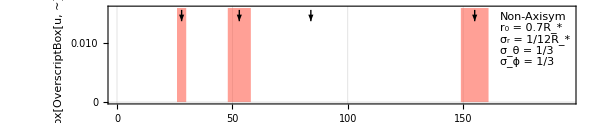

```mathematica
ymax=(*0.0000055*)0.016;
sgrplot=Show[ListLinePlot[Table[{(*10*)(sgr[1900][[i]]+(-1)^j sgrs[[i]]),21.11},{i,Length[sgr[1900]]},{j,2}],PlotRange->{{0,195(*1650*)},{0,ymax(*21*)}},
PlotStyle->Directive[PointSize[0.001]],
ImageSize->600,AspectRatio->1/(3GoldenRatio),
Filling->Axis,FillingStyle->Directive[Thickness[.03],RGBColor[1,0.32,0.25,0.55]],
(*PlotLabel->Style["External Origin",FontSize->14],*)
LabelStyle->{Directive[Black,FontFamily->Times,FontSize->12]},
GridLines->{zshift(2π τ)^-1 Flatten[Table[Re[ww[n,l]],{l,1,25},{n,1,20}]], {0}},
Frame->True,FrameTicksStyle->Directive[RGBColor[0,0,0],Thickness[.0015]],FrameStyle->Directive[Black,Thickness[.002]],
FrameLabel->{"Frequency [Hz]"(*""*),"(│ SubscriptBox[OverscriptBox[u, ~], s] │)/(R_*) √E_0"},
FrameTicks->{{(*Left*)leftticks,(*Right*)Table[If[Mod[x,(*10/10000000*)5/1000]==0,{x,"",{.015,0}},{x,"",{.005,0}}],{x,0,(*55/10000000*)20/1000,(*2/10000000*)1/1000}]},{(*Bottom*)Table[If[Mod[x, 50]==0,{x,ToString[x],{.015,0}},{x,"",{.005,0}}],{x,0,190,10}],(*Top*)Table[If[Mod[x, 50]==0,{x,"",{.015,0}},{x,"",{.005,0}}],{x,0,190,10}]}}],
Graphics[{Thick,Arrowheads[.02],
Arrow[{{sgr[1900][[1]],.98 ymax},{sgr[1900][[1]],.86ymax}}],
Arrow[{{sgr[1900][[2]],.98 ymax},{sgr[1900][[2]],.86ymax}}],
Arrow[{{sgr[1900][[3]],.98 ymax},{sgr[1900][[3]],.86ymax}}],
Arrow[{{sgr[1900][[4]],.98 ymax},{sgr[1900][[4]],.86ymax}}]}],
Graphics[{White,Rectangle[{165,.36(*.78*)ymax},{191.5(*260*),.98ymax}]}],
Graphics[{Directive[Black,FontFamily->Times,FontSize->12],
Text["Non-Axisym"(*"Axisymmetric"*),{166,.85ymax},{-1,-1}],
Text["r_0 = 0.7R_*",{166,.73ymax},{-1,-1}],
Text["σ_r = 1/12R_*",{166,.61ymax},{-1,-1}],
Text["σ_θ = 1/3",{166,.49ymax},{-1,-1}],
Text["σ_ϕ = 1/3",{166,.37ymax},{-1,-1}]}]]
```

```mathematica
Table[If[Mod[x,10/10000000(*5/1000*)]==0,{N[x],ToString[N[x]],{.015,0}},{N[x],"",{.005,0}}],{x,0,55/10000000(*200/10000*),2/10000000(*1/1000*)}]
```

```mathematica
leftticks={{0,"0",{0.015,0}},{0.001`3.,"",{0.005,0}},{0.002`3.,"",{0.005,0}},{0.003`3.,"",{0.005,0}},{0.004`3.,"",{0.005,0}},{0.005`4.,"0.005",{0.015,0}},{0.006`3.,"",{0.005,0}},{0.007`3.,"",{0.005,0}},{0.008`3.,"",{0.005,0}},{0.009`3.,"",{0.005,0}},{0.01`4.,"0.010",{0.015,0}},{0.011`3.,"",{0.005,0}},{0.012`3.,"",{0.005,0}},{0.013`3.,"",{0.005,0}},{0.014`3.,"",{0.005,0}},{0.015`4.,"0.015",{0.015,0}},{0.016,"",{0.005,0}},{0.017,"",{0.005,0}},{0.018,"",{0.005,0}},{0.019,"",{0.005,0}},{0.02,"0.020",{0.015,0}}};
```

```mathematica
leftticks={{0,"0",{0.015,0}},{2.*^-7,"",{0.005,0}},{4.*^-7,"",{0.005,0}},{6.*^-7,"",{0.005,0}},{8.*^-7,"",{0.005,0}},{1.*^-6,"10^-6",{0.015,0}},{1.2*^-6,"",{0.005,0}},{1.4*^-6,"",{0.005,0}},{1.6*^-6,"",{0.005,0}},{1.8*^-6,"",{0.005,0}},{2.*^-6,"2×10^-6",{0.015,0}},{2.2*^-6,"",{0.005,0}},{2.4*^-6,"",{0.005,0}},{2.6*^-6,"",{0.005,0}},{2.8*^-6,"",{0.005,0}},{3.*^-6,"3×10^-6",{0.015,0}},{3.2*^-6,"",{0.005,0}},{3.4*^-6,"",{0.005,0}},{3.6*^-6,"",{0.005,0}},{3.8*^-6,"",{0.005,0}},{4.*^-6,"4×10^-6",{0.015,0}},{4.2*^-6,"",{0.005,0}},{4.4*^-6,"",{0.005,0}},{4.6*^-6,"",{0.005,0}},{4.8*^-6,"",{0.005,0}},{5.*^-6,"5×10^-6",{0.015,0}},{5.2*^-6,"",{0.005,0}},{5.4*^-6,"",{0.005,0}}};
```

### Fourier Transform w/ Peak Tracing

```mathematica
Ns=10; (* Number of FT to overlap *)
ns=10; (* Number of points to drop between each FT*)
Δs=Round[1000ns Δt]/1000;
τ=.0123//N; (* Physical Timescale*)
zshift=0.766; (* Frequency red shift from GR*)
Do[
freqcutoff=100;
freqCOdimless=25(*zshift(3.5τ(tfin-ti))^-1 freqcutoff*);

Nt=(tfin-ti)/Δt(*+1*)//Round;

(*dft=Take[Fourier[δL[[;;Nt,2]]],Round[freqCOdimless(tfin-ti)]];
dfts=2 Nt^(-1/2) Abs[dft];*)
Do[
dftl[l]=Take[Fourier[(*τxsymlts*)Uϕ2lts[[;;Nt,Position[lspc,l][[1,1]],2]]],Round[freqCOdimless(tfin-ti)]];
,{l,lspc}];

dfts=2 Nt^(-1/2) Abs[Sum[dftl[l],{l,lspc}]]^(1(*2*));
dftd[Round[Ns-(tf-tfin)/Δs]]=Table[{zshift((*2.4*) τ(tfin-ti))^-1(j-1), dfts[[j]]},{j,1,Round[freqCOdimless(tfin-ti)]}];
(*Print[Round[Ns-(tf-tfin)/Δs]];*)
,{tfin,Round[tf]-(Ns) Δs,tf,Δs}];
dftc=Sort[Flatten[dftd/@Range[10],1]];
```

```mathematica
(*Outc100pst1000=*)Show[sgrplot,
ListLinePlot[dftc,Frame->True,PlotStyle->Directive[Black,Thickness[.003(*.004*)]],PlotRange->{{1,195},All},ImageSize->Full,InterpolationOrder->0,AspectRatio->1/(4GoldenRatio)]]
```

```mathematica
SetDirectory["C:\\Users\\joebr\\OneDrive\\Documents\\QPO Research\\Mathematica Plots"];
Export["PSthetadep.png",%14,ImageResolution->400]
```

PSthetadep.png